```mathematica
f[x_]=(Sinh[√(x^2+x + 5)]+π)/(√(3 x^8+11 x^4+33))
```

(π+Sinh[√(5+x+x^2)])/(√(33+11 x^4+3 x^8))

```mathematica
n=10; h=(b-a)/n;
```

```mathematica
dataApr=DataForSplain(*таблица значений функции f (x) в равноотстоящих точках отрезка[0,6],полученной в задании 1 при n=10*)
```

{{0.,1.35195},{0.6,1.50591},{1.2,1.33212},{1.8,0.685663},{2.4,0.360695},{3.,0.236911},{3.6,0.187258},{4.2,0.169776},{4.8,0.170404},{5.4,0.184714},{6.,0.212533}}

```mathematica
a11=n;(*ищем коэффициенты системы уравнений,
используя метод наименьших квадаратов,для многочлена вида kx+b*)
```

```mathematica
a12=∑_(i=1)^(n+1) dataApr[[i,1]]
```

33.

```mathematica
a21=a12
```

33.

```mathematica
a22=∑_(i=1)^(n+1) (dataApr[[i,1]])^2
```

138.6

```mathematica
b1=∑_(i=1)^(n+1) dataApr[[i,2]]
```

6.39794

```mathematica
b2=∑_(i=1)^(n+1) (dataApr[[i,1]]*dataApr[[i,2]])
```

9.79047

```mathematica
A = ({{a11, a12}, {a21, a22}})
```

{{10,33.},{33.,138.6}}

```mathematica
B =({{b1}, {b2}})
```

{{6.39794},{9.79047}}

```mathematica
coeffs = LinearSolve[A,B](*найденные коэффициенты*)
```

{{1.89787},{-0.381237}}

```mathematica
Q1[x_]=coeffs⟦2⟧*x+coeffs⟦1⟧(*многочлен,полученный результате аппроксимации*)
```

{1.89787-0.381237 x}

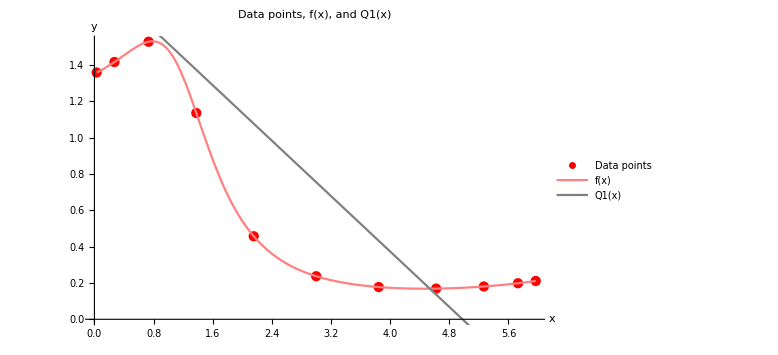

```mathematica
Show[ListPlot[data, PlotStyle-> Red, PlotLegends->{"Data points"}], Plot[f[x],{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]},PlotStyle->Pink, PlotLegends->{"f(x)"}], Plot[Q1[x],{x, Min[data⟦ All,1⟧],Max[data⟦ All,1⟧]}, PlotStyle-> Gray, PlotLegends->{"Q1(x)"}], AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and Q1(x)", ImageSize-> Large]
```

```mathematica
(*ищем коэффициенты системы уравнений,используя метод наименьших квадаратов,для многочлена вида kx2+cx+b*)a13=a22
```

138.6

```mathematica
a23 = ∑_(i=1)^(n+1) dataApr[[i,1]]^3
```

653.4

```mathematica
a31=a22
```

138.6

```mathematica
a32=a23
```

653.4

```mathematica
a33 = ∑_(i=1)^(n+1) dataApr[[i,1]]^4
```

3283.16

```mathematica
b3 = ∑_(i=1)^(n+1) (dataApr[[i,1]]^2*dataApr[[i,2]])
```

31.277

```mathematica
Clear[A]
```

```mathematica
Clear[B]
```

```mathematica
A = ({{a11, a12, a13}, {a21, a22, a23}, {a31, a32, a33}})
```

{{10,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

```mathematica
B = ({{b1}, {b2}, {b3}})
```

{{6.39794},{9.79047},{31.277}}

```mathematica
coeffs=LinearSolve[A,B](*найденные коэффициенты многочлена*)
```

{{3.90385},{-2.05288},{0.253279}}

```mathematica
Q2[x_]=coeffs⟦3⟧*x^2+coeffs⟦2⟧*x+ coeffs⟦1⟧(*многочлен,полученный результате аппроксимации*)
```

{3.90385-2.05288 x+0.253279 x^2}

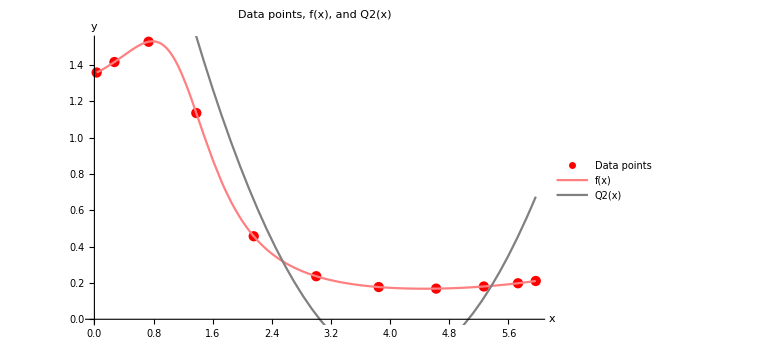

```mathematica
Show[ ListPlot[data, PlotStyle-> Red,PlotLegends->{"Data points"}],Plot[f[x],{x,Min[data⟦All,1⟧],Max[data⟦ All,1⟧]}, PlotStyle-> Pink,PlotLegends->{"f(x)"}],Plot[Q2[x],{x, Min[data⟦ All,1⟧], Max[data⟦ All,1⟧]},PlotStyle-> Gray,PlotLegends->{"Q2(x)"}], AxesLabel->{"x","y"},
 PlotLabel->"Data points, f(x), and Q2(x)",ImageSize->Large]
```

```mathematica
(*находим многочлены наилучшего среднеквадратичного приближения третьей и четвертой степеней с помощью функции согласовать Fit пакета Mathematica*)
Q3[x_]=Fit[DataForSplain,{1,x,x^2,x^3}, x]
```

1.5429-0.367874 x-0.0463432 x^2+0.0122269 x^3

```mathematica
Q3[x_]=Fit[DataForSplain,{1,x,x^2,x^3,x^4}, x]
```

1.39575+0.483684 x-0.755975 x^2+0.201462 x^3-0.0157696 x^4

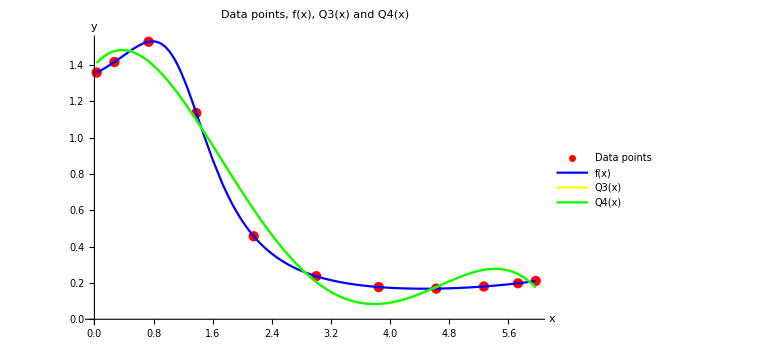

```mathematica
Show[ListPlot[data, PlotStyle->Red, PlotLegends->{"Data points"}],Plot[f[x],{x,Min[data⟦All,1⟧],Max[data⟦ All,1⟧]}, PlotStyle-> Blue, PlotLegends->{"f(x)"}],Plot[Q3[x],{x, Min[data⟦ All,1⟧], Max[data⟦ All,1⟧]}, PlotStyle-> Yellow,PlotLegends->{"Q3(x)"}],Plot[Q4[x],{x, Min[data⟦ All,1⟧], Max[data⟦ All,1⟧]}, PlotStyle-> Green, PlotLegends->{"Q4(x)"}], AxesLabel->{"x","y"}, PlotLabel->"Data points, f(x), Q3(x) and Q4(x)", ImageSize-> Large]
```

```mathematica
(*вычисляем значения функции имногочленов в точке x=2.4316*)f[2.4316]
Q1[2.4316]
Q2[2.4316]
Q3[2.4316]
Q4[2.4316]
```

0.350875

{0.97086}

{0.409623}

0.447214

0.447214

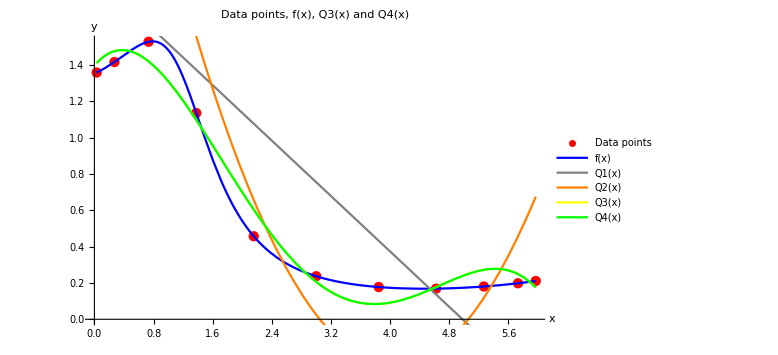

```mathematica
Show[ ListPlot[data,PlotStyle->Red, PlotLegends->{"Data points"}],Plot[f[x],{x, Min[data⟦ All,1⟧], Max[data⟦All,1⟧]}, PlotStyle-> Blue, PlotLegends->{"f(x)"}],Plot[Q1[x],{x, Min[data⟦ All,1⟧],Max[data⟦ All,1⟧]},PlotStyle-> Gray, PlotLegends->{"Q1(x)"}],Plot[Q2[x],{x, Min[data⟦ All,1⟧],Max[data⟦All,1⟧]}, PlotStyle-> Orange, PlotLegends->{"Q2(x)"}], Plot[Q3[x],{x, Min[data⟦ All,1⟧],Max[data⟦ All,1⟧]}, PlotStyle->Yellow, PlotLegends->{"Q3(x)"}], Plot[Q4[x],{x, Min[data⟦ All,1⟧],Max[data⟦ All,1⟧]},PlotStyle-> Green,PlotLegends->{"Q4(x)"}], AxesLabel->{"x","y"}, PlotLabel->"Data points, f(x), Q3(x) and Q4(x)", ImageSize-> Large]
```

```mathematica
(*Вывод:чем выше степень многочлена,тем ближе к данному графику функции мы получаем приближение*)
```